A Study In Proof Space Topology 
Richard James Charette
University of Massachusetts Dartmouth, mentor James Boyd@WSS,2022

Abstract
The goal of this project is to advance our understanding of axiom systems by methodically enumerating possible axiom systems and computing their entailment cones under both non-accumulative and accumulative conditions. By utilizing substitution and co-substitution techniques from various initial conditions, we aim to explore the structural properties of these systems.

The entailment cones, which represent the space of consequences derivable from a set of axioms, are analyzed to uncover their topological features. To achieve this, we will enumerate proof paths within these cones and apply methods from homology and homotopy theory to provide a deeper topological insight. This approach allows for a comprehensive examination of the interplay between different axiom systems and their logical consequences. Through this analysis, we seek to map out the intricate landscape of axiom systems, shedding light on their foundational structure and the nature of their derivable truths. The project will contribute to the broader field of mathematical logic and theoretical computer science, offering new perspectives on the formulation and implications of axiomatic systems.

Introduction

In pure mathematics, our overarching aim is to establish the foundational theorems that underpin further mathematical developments. These foundational theorems serve as essential building blocks for a wide array of mathematical structures and concepts. The primary objective is the formulation and comprehension of these theorems, rather than merely focusing on the specific proofs that derive them. While this approach may initially appear counterintuitive, it is essential to recognize the distinctive nature of metamathematics.

Metamathematics, a branch of mathematical logic, prioritizes the study of theorems and the formal systems that produce them. The main goal in metamathematics is not just to prove individual theorems but to analyze and understand the overall structure and properties of theorems within a given formal system. This involves examining the processes by which theorems are derived, including the rules of inference, axioms, and the logical frameworks employed.

In this project, we aim to contribute to the field of metamathematics by exploring axiom systems and their entailment cones, both non-accumulative and accumulative, through the use of substitution and co-substitution techniques from different initial conditions. By enumerating possible axiom systems and computing their entailment cones, we intend to uncover the structural and topological characteristics of these systems. We will enumerate proof paths within these cones and apply methods from homology and homotopy theory to gain deeper insights into their topological features. This approach will help us understand the intricate landscape of axiom systems and the logical consequences they produce, thereby shedding light on the nature of mathematical truth and the process of theorem generation.

Our work aims to bridge the gap between pure mathematics and metamathematics, providing a comprehensive framework for studying the structure of theorems and the processes by which they are derived. This, in turn, will enhance our understanding of the foundations of mathematics and contribute to the advancement of mathematical logic and theoretical computer science.

Specifically, the goal of this project is to understand simple axiom systems by laying the groundwork for how theorems are solved. We employ a two-way system with arbitrary rules defined from A ⟷ A to BBB⟷BBB. By utilizing a proof path graph through multiple iterations, we generate various sample types where cycles are defined through a cycle graph, outlining the proofs. Using a graph union, we identify all cycles attached to the base axiom, thereby proving the structure and revealing its topological features. Subsequently, the entailment cone is computed using both substitution and co-substitution from different initial conditions.

Section I: Accumulative Entailment Structures

The entailment is a fundamental concept that describes the logical relationship between statements that hold the premise of either being true or false and that yields a valid argument in-which the conclusion of said logical argument holds logical structures that are built upon. From this, there can only be a conclusion that is entailed by its premise; this is because such a conclusion would have to hold a premise because of being a logical argument.

Partially explained earlier in the introduction, these are the rules stated below. The rules are the axiom systems that contain the two-way systems that will be used and define the experiment. First off, the code used defines axioms 1 through 196 (it should be noted for later reference that as we use these axioms, not all of them will be used), which for this case is used throughout this study. These rules list all axiom systems going down the list. These axioms will further the study as we continue in Section II by using these axioms’ proof graphs.  These are the basis for the project and are used for the theorems.

```mathematica
rules=Grid[Partition[Take[Flatten[With[{strings=Flatten[Table[StringJoin[#]&/@Tuples[{"A","B"},i],{i,1,3}]]},Table[strings[[i]]<->strings[[j]],{i,1,Length[strings]},{j,1,Length[strings]}]]],100],10],Frame->All,Background->Lighter[{{"[◼]", "MetamathematicsStyleData"}}["AxiomColor"],.8],FrameStyle->GrayLevel[.75],ItemStyle->{{"[◼]", "MetamathematicsStyleData"}}["AxiomFontColor"],Spacings->1]
```

A<->A | A<->B | A<->AA | A<->AB | A<->BA | A<->BB | A<->AAA | A<->AAB | A<->ABA | A<->ABB
A<->BAA | A<->BAB | A<->BBA | A<->BBB | B<->A | B<->B | B<->AA | B<->AB | B<->BA | B<->BB
B<->AAA | B<->AAB | B<->ABA | B<->ABB | B<->BAA | B<->BAB | B<->BBA | B<->BBB | AA<->A | AA<->B
AA<->AA | AA<->AB | AA<->BA | AA<->BB | AA<->AAA | AA<->AAB | AA<->ABA | AA<->ABB | AA<->BAA | AA<->BAB
AA<->BBA | AA<->BBB | AB<->A | AB<->B | AB<->AA | AB<->AB | AB<->BA | AB<->BB | AB<->AAA | AB<->AAB
AB<->ABA | AB<->ABB | AB<->BAA | AB<->BAB | AB<->BBA | AB<->BBB | BA<->A | BA<->B | BA<->AA | BA<->AB
BA<->BA | BA<->BB | BA<->AAA | BA<->AAB | BA<->ABA | BA<->ABB | BA<->BAA | BA<->BAB | BA<->BBA | BA<->BBB
BB<->A | BB<->B | BB<->AA | BB<->AB | BB<->BA | BB<->BB | BB<->AAA | BB<->AAB | BB<->ABA | BB<->ABB
BB<->BAA | BB<->BAB | BB<->BBA | BB<->BBB | AAA<->A | AAA<->B | AAA<->AA | AAA<->AB | AAA<->BA | AAA<->BB
AAA<->AAA | AAA<->AAB | AAA<->ABA | AAA<->ABB | AAA<->BAA | AAA<->BAB | AAA<->BBA | AAA<->BBB | AAB<->A | AAB<->B

Table I: This table shows most cases used in this study with emissions of 101 through 196 for the sake of showcasing.

```mathematica
With[{rules=Take[Flatten[With[{strings=Flatten[Table[StringJoin[#]&/@Tuples[{"A","B"},i],{i,1,3}]]},Table[strings[[i]]<->strings[[j]],{i,1,Length[strings]},{j,1,Length[strings]}]]],{6,8}]},Labeled[{{"[◼]", "TwoWayStringTokenEventGraph"}}[{#},2,"Sorting"->True,ImageSize->Medium,],Text[Style[#,GrayLevel[.4],Medium]]]&/@rules]
```

-Graphics-

Section II: The Proof Path Graphs
The proof graphs here are based on sample rules 3, 4, 25, 100, 140, and 195. The rules selected have no real value outside showing the proof graphs and showing the interconnection of the axioms with each other. I am sure something well noted in all the sample rules is a small red line. That is simple proof and is not used in spokes graphs to show a cycle. As for the rest of the graphs, they all show the cycles and possibilities that show the axioms that make a theorem. In later sections, we will even take a random sample and show off the cycles in these graphs that can further show the organization.

I find it intrusting just looking at the graphs how the formal structure is the same as the axioms maintain an exact similar structure; I am not sure why that is, but is it something that I noted in this survey and the fact that these listings prove it must have something to do with the similarities if a rule is closer together, for example, rule 3 and 4 are next to each other, while rule 3 and 195 have hundreds of rules of separation between each other that the similarities are not there.

A good thing to note is the sink vertex. What is the sink vertex? It is the vertex (or node) that is computed (connected) by other vertexes that leads to it being connected. In our case here the vertex sink is where all the edges point to that leads to the answer, which if I take an example case from rule 3 would look like this: A<->AA → A<->AAA, so the lead vertex ends at the sink, which is the answer.

Just to showcase again rule 3’s proof path again with no labels.

```mathematica
rules=Flatten[With[{strings=Flatten[Table[StringJoin[#]&/@Tuples[{"A","B"},i],{i,1,3}]]},Table[strings[[i]]<->strings[[j]],{i,1,Length[strings]},{j,1,Length[strings]}]]];h={{"[◼]", "TwoWayStringTokenEventGraph"}}[{rules[[3]]},3,"Sorting"->True,];
vertlist=DeleteCases[DeleteCases[#,_Integer]&/@VertexList[h],x_/;ResourceFunction["ContainsQ"][x,"Event"]];graphs=Table[Module[{proofs},
proofs={{"[◼]", "LiteralizeTwoWayRules"}}/@{{"[◼]", "FindTokenEventProof"}}[h,{rules[[3]]},vertlist[[i]],8];
proofgraphs=VertexPop[#,{"Event",___}]&/@proofs;
HighlightGraph[GraphUnion@@proofgraphs,proofgraphs]],{i,2,Length[vertlist]}]
```

-Graphics-

```mathematica
rules=Flatten[With[{strings=Flatten[Table[StringJoin[#]&/@Tuples[{"A","B"},i],{i,1,3}]]},Table[strings[[i]]<->strings[[j]],{i,1,Length[strings]},{j,1,Length[strings]}]]];
h={{"[◼]", "TwoWayStringTokenEventGraph"}}[{rules[[25]]},3,"Sorting"->True,];
vertlist=DeleteCases[DeleteCases[#,_Integer]&/@VertexList[h],x_/;ResourceFunction["ContainsQ"][x,"Event"]];Table[Module[{h={{"[◼]", "TwoWayStringTokenEventGraph"}}[{rules[[25]]},3,"Sorting"->True,],proofs},
proofs={{"[◼]", "LiteralizeTwoWayRules"}}/@{{"[◼]", "FindTokenEventProof"}}[h,{rules[[25]]},vertlist[[i]],8];
proofgraphs=Graph[#]&/@proofs;
HighlightGraph[GraphUnion@@proofgraphs,proofgraphs]],{i,2,Length[vertlist]}]
```

-Graphics-

```mathematica
rules=Flatten[With[{strings=Flatten[Table[StringJoin[#]&/@Tuples[{"A","B"},i],{i,1,3}]]},Table[strings[[i]]<->strings[[j]],{i,1,Length[strings]},{j,1,Length[strings]}]]];VertexPop[g_, patt_, opts___] := EdgeAdd[VertexDelete[g,patt],Catenate[DirectedEdge@@@Tuples[{VertexInComponent[g,#,{1}],VertexOutComponent[g,#,{1}]}]&/@VertexList[g,patt]], opts, Options[g]];h={{"[◼]", "TwoWayStringTokenEventGraph"}}[{rules[[3]]},3,"Sorting"->True,];
vertlist=DeleteCases[DeleteCases[#,_Integer]&/@VertexList[h],x_/;ResourceFunction["ContainsQ"][x,"Event"]];graphs=Table[Module[{proofs},
proofs={{"[◼]", "LiteralizeTwoWayRules"}}/@{{"[◼]", "FindTokenEventProof"}}[h,{rules[[3]]},vertlist[[i]],8];
proofgraphs=VertexPop[#,{"Event",___}]&/@proofs;
UndirectedGraph[HighlightGraph[GraphUnion@@proofgraphs,proofgraphs]]],{i,2,Length[vertlist]}]
```

-Graphics-

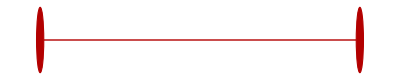
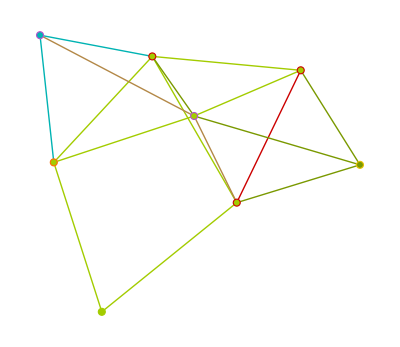
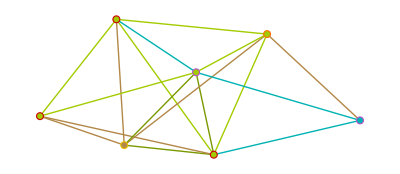
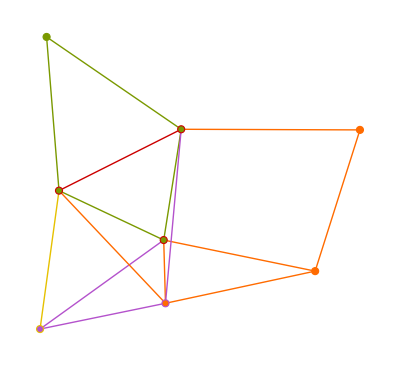
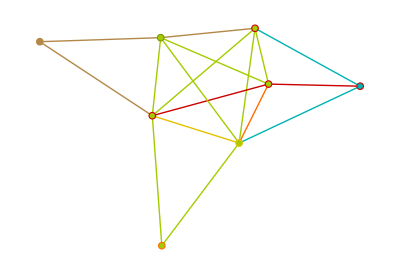
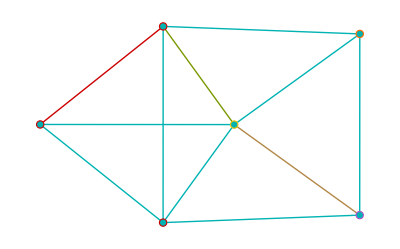
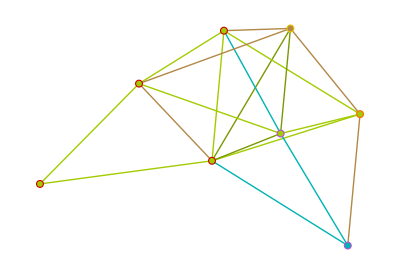
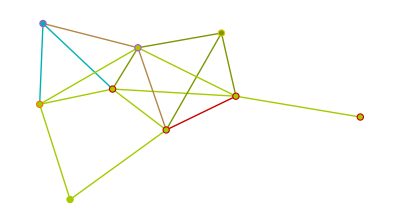
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
rules=Flatten[With[{strings=Flatten[Table[StringJoin[#]&/@Tuples[{"A","B"},i],{i,1,3}]]},Table[strings[[i]]<->strings[[j]],{i,1,Length[strings]},{j,1,Length[strings]}]]];VertexPop[g_, patt_, opts___] := EdgeAdd[VertexDelete[g,patt],Catenate[DirectedEdge@@@Tuples[{VertexInComponent[g,#,{1}],VertexOutComponent[g,#,{1}]}]&/@VertexList[g,patt]], opts, Options[g]];h={{"[◼]", "TwoWayStringTokenEventGraph"}}[{rules[[25]]},3,"Sorting"->True,];
vertlist=DeleteCases[DeleteCases[#,_Integer]&/@VertexList[h],x_/;ResourceFunction["ContainsQ"][x,"Event"]];graphs=Table[Module[{proofs},
proofs={{"[◼]", "LiteralizeTwoWayRules"}}/@{{"[◼]", "FindTokenEventProof"}}[h,{rules[[25]]},vertlist[[i]],8];
proofgraphs=VertexPop[#,{"Event",___}]&/@proofs;
UndirectedGraph[HighlightGraph[GraphUnion@@proofgraphs,proofgraphs]]],{i,2,Length[vertlist]}]
```

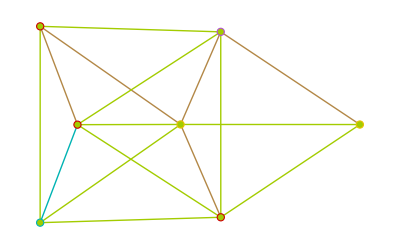
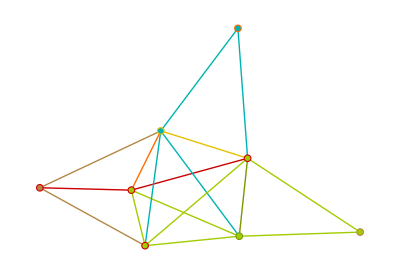
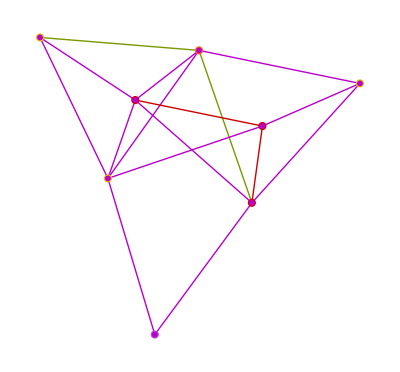
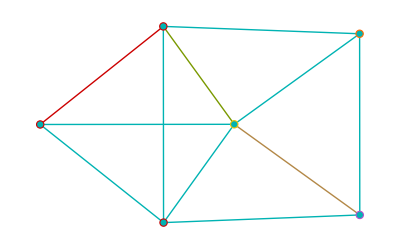
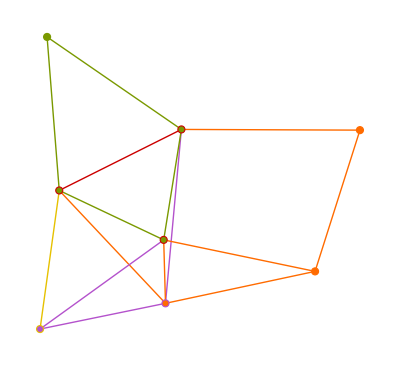
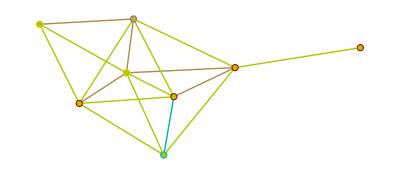
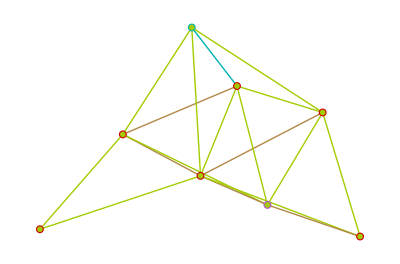
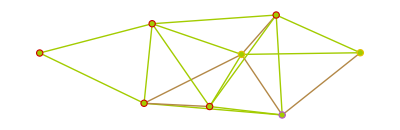
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
rules=Flatten[With[{strings=Flatten[Table[StringJoin[#]&/@Tuples[{"A","B"},i],{i,1,3}]]},Table[strings[[i]]<->strings[[j]],{i,1,Length[strings]},{j,1,Length[strings]}]]];VertexPop[g_, patt_, opts___] := EdgeAdd[VertexDelete[g,patt],Catenate[DirectedEdge@@@Tuples[{VertexInComponent[g,#,{1}],VertexOutComponent[g,#,{1}]}]&/@VertexList[g,patt]], opts, Options[g]];h={{"[◼]", "TwoWayStringTokenEventGraph"}}[{rules[[100]]},3,"Sorting"->True,];
vertlist=DeleteCases[DeleteCases[#,_Integer]&/@VertexList[h],x_/;ResourceFunction["ContainsQ"][x,"Event"]];graphs=Table[Module[{proofs},
proofs={{"[◼]", "LiteralizeTwoWayRules"}}/@{{"[◼]", "FindTokenEventProof"}}[h,{rules[[100]]},vertlist[[i]],8];
proofgraphs=VertexPop[#,{"Event",___}]&/@proofs;
UndirectedGraph[HighlightGraph[GraphUnion@@proofgraphs,proofgraphs]]],{i,2,Length[vertlist]}]
```

Section III: Fundamental group

Spoke graphs shows all cycles possible that are attached at the base axiom, which is really amazing how all this information is compact into such a graph that the inner defined part of the spoke has all this information around it, and how they form the cycles that go around it from the rules. Now, one of the interesting aspects of this graph is how spokes on the graph vary by cycle length as it goes around to complete a circuit and how chaotic it is in its organization.

Speaking of the cycle, I am assuming clarification needs to be brought to of what is talked about in order to understand fully. A cycle or better known as a cyclic permutation is a type of permutation that is set to the elements of the various set with X. For this case, in particular, X is mapped with the elements of a subset S of X, and it is mapped in a manner that is cyclic in nature where the elements of a subset S of X onto each other in a cyclic manner. When a typing of mapping called fixing involves the other elements that are contained in X. What that means for the subset of S of X is it has could have elements of its own, so so if that is the case then S has k elements and this type of cycle is known as the k-cycle. These types of cycles are mostly given a denotation by the list of enclosed parenthesis for it to be permutated.     

To better understand what was stated in the previous paragraph, the basic formulas to compute these cycles can be expressed as basic symmetric groups, for these cases they are cyclic. Since these cycles are self-commuting, the expressions have a unique order in the cycles. From this, we can fully determine the various cycle lengths, which also determine the permutation. 

Taking the number of k-cycles in a symmetric group for S_n that is given by the following: 

     (n
k)(k-1)!= (n(n-1)....(n-k+1))/k= (n!)/((n-k)!k)

```mathematica
HighlightGraph[Graph[EdgeList[graphs[[5]]],VertexShapeFunction->"Rectangle",VertexSize->.75,ImageSize->Medium,VertexLabels->Placed[Automatic,Center],VertexStyle->{"A"↔"AA"->Lighter[{{"[◼]", "MetamathematicsStyleData"}}["AxiomColor"],.6],Lighter[{{"[◼]", "MetamathematicsStyleData"}}["TheoremColor"],.6]}],FindCycle[graphs[[5]],{Length[VertexList[graphs[[5]]]]}]]
```

-Graphics-

```mathematica
Table[Graph[Flatten[Take[cycles,{i}]],VertexStyle->{First[First[Flatten[Take[cycles,{i}]]]]->Lighter[{{"[◼]", "MetamathematicsStyleData"}}["AxiomColor"],.6],Lighter[{{"[◼]", "MetamathematicsStyleData"}}["TheoremColor"],.6]},VertexShapeFunction->"Rectangle",VertexSize->.65,ImageSize->Medium,VertexLabels->Placed[Automatic,Center]],{i,7,9}]
```

-Graphics-

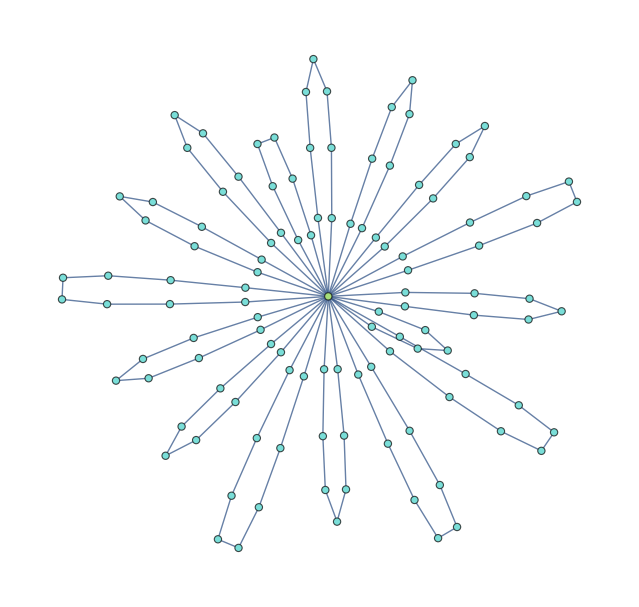

```mathematica
Graph[GraphUnion@@MapIndexed[VertexReplace[Graph[Flatten[#]],v:Except["A"↔"AA"]:>{v,#2[[1]]}]&,cycles],VertexStyle->{"A"↔"AA"->{{"[◼]", "MetamathematicsStyleData"}}["AxiomColor"],{{"[◼]", "MetamathematicsStyleData"}}["TheoremColor"]}]
```

The fundamental group is the group of the equivalence classes that is under homotopy with various loops attached to it that is contained within a space. The shape, size, and various other information is recorded and maintained and contained in topological space.  Now, the fundamental group for this case is the homotopy invariant, so this means they are typological spaces that are homotopy equivalent that are apart of the fundamental group. The fundamental group of topological spaces is thus defined by X as denoted by π_1(X).

For the loop in our cases it is tied at the center axiom and pivots each loop on it, but for our case we can see it just a base example multiple figure eight loops, so by the fundamental group of the figure eight has to be a free group on two letters. To prove this we start by proving that the eight circles, so the loop we defined will be ω as the whole graph with a^n_1 b^m_1 to a^n_8 b^m_8 are the loops.

As we connect all the loops together each loop forms a figure eight, and as a while all the loops form form ω for the total of all; it should be noted that in order for this graph to even be this shape it must not abelian, so we must not get any commutative properties as a result of this graph. The interconnectivity of both loops for each pair is done by the fundamental group for the wedge sum, as each loop is divided in half by its wedge were we get X for one side and Y for the other. 

What we see in this graph that I wish to explore more is the size of each loop as it goes through the wedges, now, it makes sense as to why the size of the graph corresponds to the length since it is showing from previous explanations and examples that each axiom is solving logically as it solved the problem. Not each loop needs to be solved at similar length as others, so things are far shorter, but knowing more examples is the next step I feel.

Concluding Remarks

The summary for the results needs more work, but the present data for cycles suggests that the current results show underlining features that correlate with Boolean and other systems in how proofs are found. Still, I have not done this yet, and want to statistically show the results of which cycles will be are various rules and compare each cycle.

More work needs to be done in collecting large sample sizes and more data on different axiom systems the work needs to ensure that the data has a far larger sample size, as well as trying to establish a theorem for why these axioms in cycles act the way they do. More should be done also to understand in certain cases why disjointed unions exist in a union graph, and establish if it is a mere error, or if something else is going on mathematically. On a personal note, I need to get better at the Wolfram language, but I plan on this march to understand what is going on as I am determined to make this into a proper research paper.

One challenge I failed to complete during the Wolfram Summer program was take the entailment structure and contract equivalences to points and study structure of points, which I am determined to do later.

Keywords

•Two-way

•Proof Paths

•Entailment Cone

•Proof Space

•Cycle

Acknowledgment

•A lot help was given by James Boyd and Nik Murzin along with Stephen Wolfram for defining the direction of this project.

References

•James Boyd for all the help he has given me from coding, to understanding the Wolfram language and taking the time to explain everything from entailment cones to proof paths.

•Nik Murzin for taking time out of his day to join us at weird hours to go over issues both James and I are having with the code I did.

•Wolfram website for aiding me in my coding when not aided by either Nik or James, and for explaining a lot of terms and terminology that I may have missed in the lecture or needed to understand for my project.